```mathematica
angle[l_]:=VectorAngle[l[[2]]-l[[1]],l[[3]]-l[[1]]]
newpt[base_,oldspiral_,th_,d_]:=Exp[I(Arg[oldspiral]+th)]d
Manipulate[
pts=Table[{Cos[2Pi t/n],Sin[2 Pi t/n],h t/n},{t,0,n}];
surface=Join[
Table[{1,i,i+1},{i,2,n}],Table[{n+1,n-i+1,n-i},{i,1,n-1}]];
flatsurface= Join[Table[ {1, i, i+1}, {i, 2, n}], Table[ {n+2, n+2+i, n+3+i}, {i, 1, n-1}]];
surfacepts=Map[pts[[#]]&,surface,{2}];
unfoldhalf=Join[{{0,0}},{-Re[#],Im[#]}&/@FoldList[newpt[0,#1,angle[surfacepts[[#2]]],EuclideanDistance[surfacepts[[#2]][[1]],surfacepts[[#2]][[3]]]]&,EuclideanDistance[surfacepts[[1]][[2]],surfacepts[[1]][[3]]],Range[1,n-1]]//N];
unfold = Flatten[{unfoldhalf,(unfoldhalf[[-1]]+#)&/@-unfoldhalf}, 1];
flatsurfacepts = Map[unfold[[#]] &, flatsurface, {2}];
Graphics3D[Polygon[surfacepts],ImageSize->Medium]
Graphics[{EdgeForm[Thin],Pink, Polygon[flatsurfacepts]},ImageSize->Medium
]
,{n,10,200,10},{h,1,17,1}]
```

```mathematica
(*Here t is from 0 to 1*)
r[h_][t_]:=√(h^2 (-1+t)^2+Sin[2π t]^2+(1-Cos[2 π t])^2)
th[h_][t_]:=NIntegrate[(√(h^2+4 π^2-(r[h]'[x])^2))/(r[h][x]), {x, 0, t}]
vertexangle[h_]:=th[h][1]+ArcTan[2Pi/h]
```

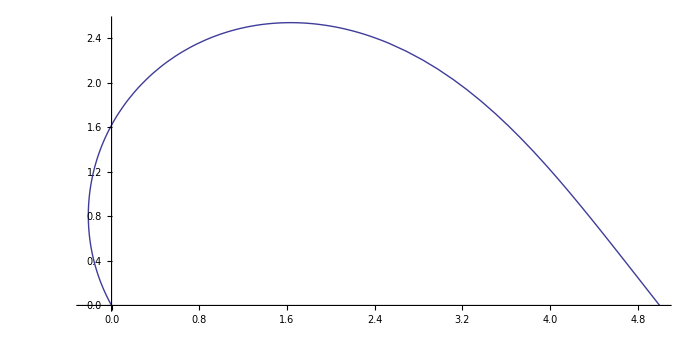

```mathematica
Module[{h=5},ParametricPlot[ {r[h][t]Cos[N[th[h][t]]],r[h][t]Sin[N[th[h][t]]]}, {t, 0, 1}]]
```

```mathematica
vertexangle[4.5520]
```

3.14159